```mathematica
ClearAll["Global`*"]
```

```mathematica
TagList ={"#boston","#bostonmarathon","#bostonstrong","#prayforboston"};
PlotType={VC,VID,CC,GD,GR,GCC,GA,MND,MDC};
S[x_]:=StringSplit[StringReplace[x,{"\""->""}]," -> "];
Fdate[x_]:=DateString[{2013,4,15,(5+x),0,0},{"DayNameShort","Hour12","AMPMLowerCase"}];
Cdate[x_]:=DateString[{2013,4,15,(5+x),0,0}];
Ldate[x_]:=ToString[DateList[{2013,4,8,(x-1),0,0}]]
LFdate[x_]:=DateList[{2013,4,8,(x-1),0,0}]
```

#### Imports data from files then anaylsises it for 9 charectoristics.

```mathematica
L=504;
For[n=1,n≤4,n++,
T=TagList[[n]];
For[i=1,i≤L,i++,
file="/Users/danielgladstone/Documents/twitter_project/FullView/"<>T<>"/"<>Ldate[i];

If[FileExistsQ[file],

F =Import[file,"List"];

GList[T][i]=DeleteDuplicates[Table[
joined=First[S[F[[j]]]]->Last[S[F[[j]]]]
,{j,1,Length[F]}]];
If[Length[GList[T][i]]≤1,

(*Print["Zero: n="<>ToString[n]<>". i="<>ToString[i]];*)

G[T][i]=0;
G[VC][T][i]=0;
G[VID][T][i]=0;
G[CC][T][i]=0;
G[GD][T][i]=0;
G[GR][T][i]=0;
G[GCC][T][i]=0;
G[GA][T][i]=0;
G[MND][T][i]=0;
G[MDC][T][i]=0;,

G[T][i]=Graph[GList[T][i]];
G[VC][T][i]=VertexCount[G[T][i]];
G[VID][T][i]=Mean[VertexInDegree[G[T][i]]];
G[CC][T][i]=Mean[ClosenessCentrality[G[T][i]]];
G[GD][T][i]=GraphDensity[G[T][i]];
G[GR][T][i]=GraphReciprocity[G[T][i]];
G[GCC][T][i]=GlobalClusteringCoefficient[G[T][i]];
G[GA][T][i]=GraphAssortativity[G[T][i]];
G[MND][T][i]=Mean[MeanNeighborDegree[G[T][i]]];
G[MDC][T][i]=Mean[MeanDegreeConnectivity[G[T][i]]];
];
,
G[T][i]=0;
G[VC][T][i]=0;
G[VID][T][i]=0;
G[CC][T][i]=0;
G[GD][T][i]=0;
G[GR][T][i]=0;
G[GCC][T][i]=0;
G[GA][T][i]=0;
G[MND][T][i]=0;
G[MDC][T][i]=0;]
]]
```

#### Iterate over data to become listed and graphable data.

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type*)

GT=PlotType[[p]];

data=
Table[
T=TagList[[n]];(*What hashtag are we looking at*)
Table[
G[GT][T][i],{i,L}] (*Iterate over every time period*)
,{n,1,4}]; (*Iterate over each hashtag*)

Data[GT]=data; (*list of data for a given graph type in with composed of smaller list for each hashtag*)
]
```

#### Iterate over data and time to become listed and graphable data with time on X-axis.

```mathematica
For[p=1,p≤9,p++,(*iterate over each graph type*)

GT=PlotType[[p]];

Tdata=Table[(*iterate over each tag*)
Table[(*iterate over each date**)
{LFdate[i],Data[GT][[n]][[i]]}
,{i,L}]
,{n,4}];
TData[GT]=Tdata;
]
```

#### Finds a function which corresponds to the 4 hashtags and 9 charectoristics associated with each tag.

```mathematica
For[p=1,p≤9,p++,(*iterate over each data type basicly decomposing the previous Data*)

GT=PlotType[[p]];

fun=
Table[
Fit[
Table[
{i,Data[GT][[n]][[i]]},{i,L}](*Iterate over every time period*)
,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11},x](*how to find line in data*)
,{n,4}];(*iterate over each hashtag*)
Fun[GT]=fun;
]
```

#### Plots data with time axis.

```mathematica
PlotTime=Table[
GT=PlotType[[p]];
DateListPlot[
Table[TData[GT][[n]],{n,4}],{LFdate[1],LFdate[L]},PlotLegends->TagList,PlotLabel->GT,Joined->True,Filling->Bottom],{p,9}];
```

#### Plots the data and corresponding functions.

```mathematica
PlotFunction=Table[
GT=PlotType[[p]];
f=Fun[GT];
Plot[f,{x,0,L},PlotLegends->TagList, PlotLabel->GT],{p,9}];
```

#### Plots of the values produced from each metrics corresponding function.

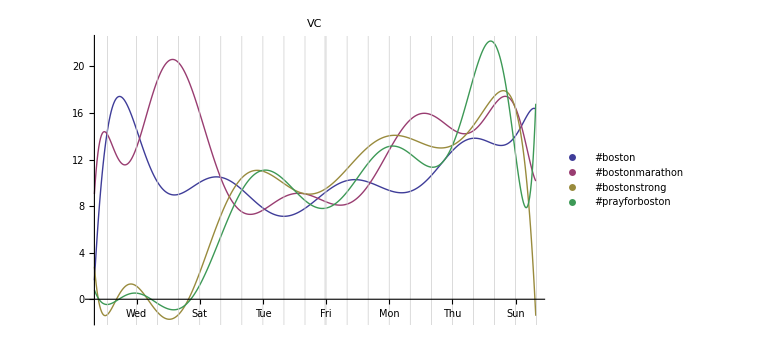
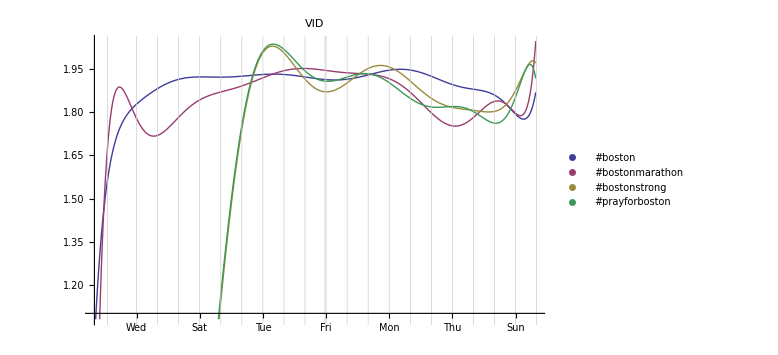
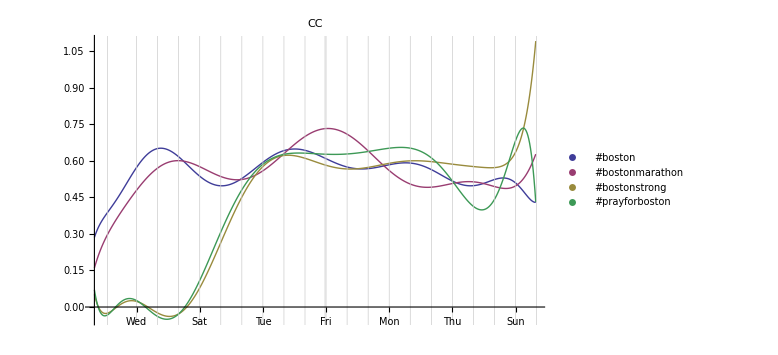
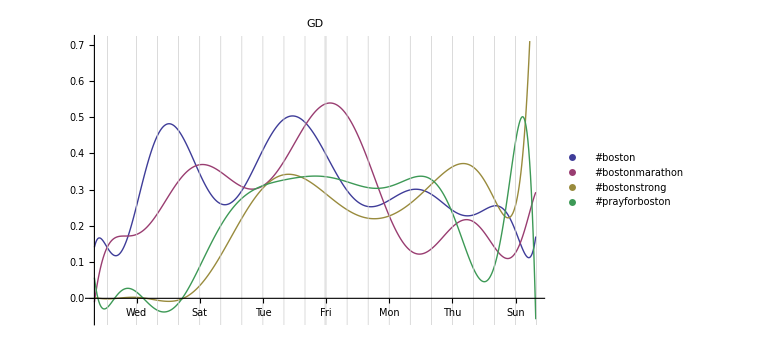
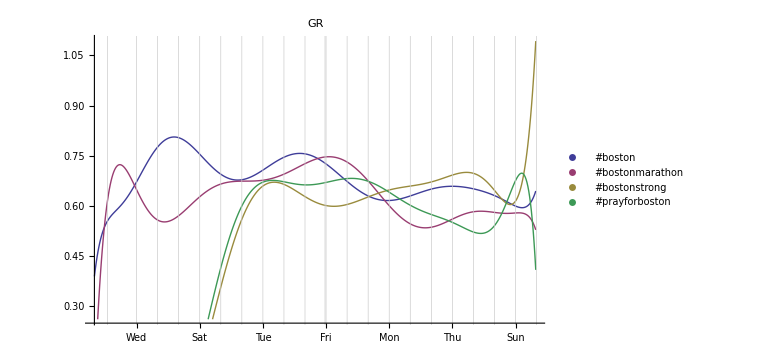
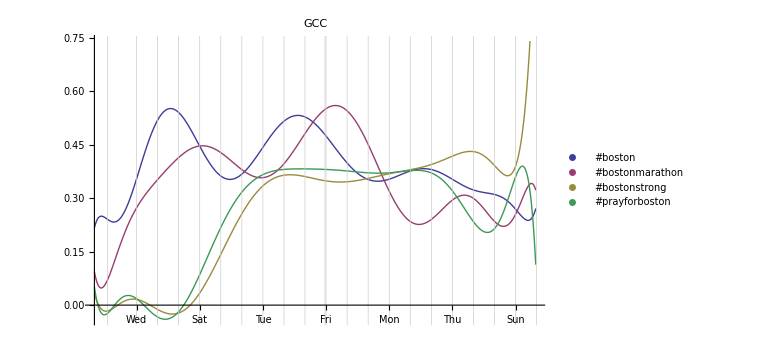
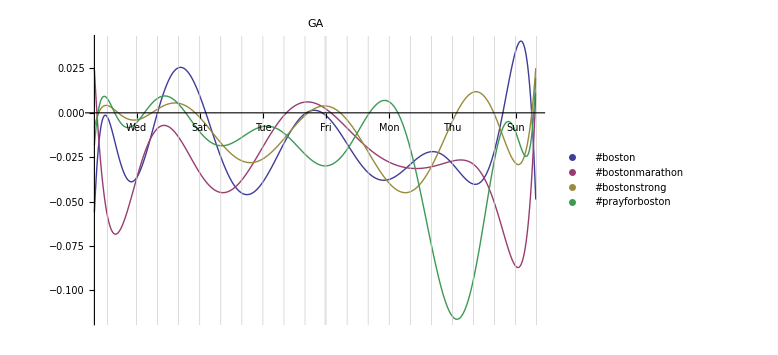
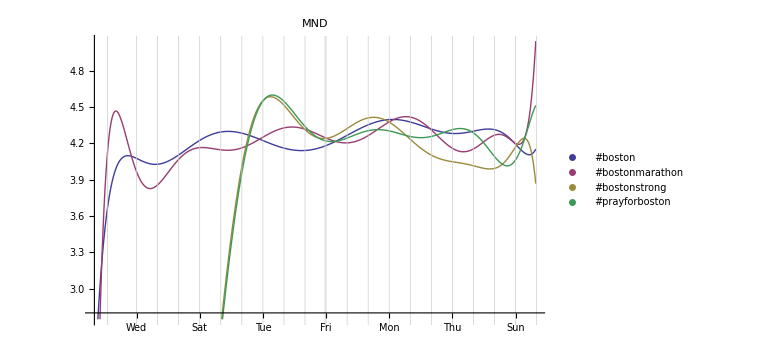

```mathematica
b=DateString[{2013,4,8,14,49,0}];
s=DateString[{2013,4,18,22,48,0}];
ticks={Join[Table[DateString[{2013,4,(8+i),0,0,0}],{i,0,21}],{{s,"Shooting",.05,Red}},{{b,"Bombing",.05,Red}}],Automatic};
dlp[x_]:=DateListPlot[x,Joined->True,PlotLegends->TagList, PlotLabel->GT,DateTicksFormat->{"DayNameShort"},Ticks->ticks,Axes->True,Frame->False,ImageSize->Large]

Table[(*iterate over each graph metric*)
dlp[GT=PlotType[[p]];
f=Fun[GT];
Table[(*iterate over each hasghtag*)
Table[(*iterate over each time period*)
{LFdate[x],f[[n]]},
{x,L}],
{n,4}]],{p,9}]
```